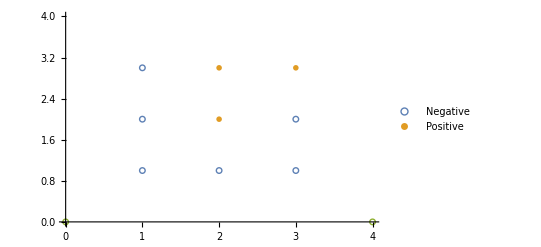

```mathematica
data:={{1,1,0},{1,2,0},{1,3,0},{2,1,0},{2,2,1},{2,3,1},{3,1,0},{3,2,0},{3,3,1}}
positive:={}
negative:={}
For[a=1,a≤Length[data],If[data[[a]][[3]]==1,positive=Append[positive,data[[a]][[1;;2]]],negative=Append[negative,data[[a]][[1;;2]]]];a+=1]
ListPlot[{negative,positive,{{0,0},{4,0}}},PlotMarkers->{○,X},PlotLegends->{"Negative","Positive"},PlotRange->4]
(*Preprocessing xs. Here x should b a vector*)
preprocess[x_]:={x[[1]],Power[x[[1]],2]*x[[2]],Power[x[[2]],2],x[[1]]*0+1}
(*So it means that h(x) is always kept in an abstract form? I think the answer is yes, at least now.*)
h[x_,θ_]:=Dot[θ,x]
(*x should always be a vector (n by 1)*)
dataX:=preprocess[data[[1;;2]]]
dataY:=data[[3]]
```

```mathematica
(*Use a polynomial of x1 and x2: x1 + x1^2*x2 + x2^2 as the hypothesis. The amount of thetas should be 4, and x1, x2 should be preprocessed into the form of 3 inputs before being applied to the hypothesis*)
```

```mathematica
θ:={0,0,0,0}
α:=0.03
epochs:=3000
(*(batch) gradient descent starts here*)
Do[
(*here the result of h should be a 1-by-n matrix*)
(θ=θ-α*(1/Length[dataX])*Dot[dataX,h[dataX,θ]-dataY]);
If[Mod[a,100]==0,Print["now epoch "<>ToString[a]<>", theta is"<>ToString[θ]]],{a,1,epochs}]
```

now epoch 100, theta is{0.134552, 0.276044, 0.559028, 0.0617412}

now epoch 200, theta is{0.12932, 0.276881, 0.572005, 0.0258628}

now epoch 300, theta is{0.130282, 0.278533, 0.575035, 0.012979}

now epoch 400, theta is{0.132578, 0.28011, 0.575172, 0.00774641}

now epoch 500, theta is{0.134819, 0.281409, 0.574591, 0.00521494}

now epoch 600, theta is{0.136678, 0.282429, 0.573932, 0.00374936}

now epoch 700, theta is{0.13814, 0.283214, 0.573362, 0.002781}

now epoch 800, theta is{0.139266, 0.283813, 0.572907, 0.00209132}

now epoch 900, theta is{0.140127, 0.28427, 0.572555, 0.00158196}

now epoch 1000, theta is{0.140782, 0.284617, 0.572286, 0.00119962}

now epoch 1100, theta is{0.141281, 0.28488, 0.57208, 0.000910639}

now epoch 1200, theta is{0.141659, 0.285081, 0.571923, 0.000691569}

now epoch 1300, theta is{0.141947, 0.285233, 0.571805, 0.000525296}

now epoch 1400, theta is{0.142166, 0.285349, 0.571714, 0.00039903}

now epoch 1500, theta is{0.142332, 0.285437, 0.571646, 0.000303124}

now epoch 1600, theta is{0.142458, 0.285503, 0.571593, 0.000230272}

now epoch 1700, theta is{0.142554, 0.285554, 0.571554, 0.00017493}

now epoch 1800, theta is{0.142627, 0.285593, 0.571524, 0.000132889}

now epoch 1900, theta is{0.142682, 0.285622, 0.571501, 0.000100951}

now epoch 2000, theta is{0.142724, 0.285644, 0.571483, 0.0000766897}

now epoch 2100, theta is{0.142756, 0.285661, 0.57147, 0.0000582588}

now epoch 2200, theta is{0.14278, 0.285674, 0.57146, 0.0000442574}

now epoch 2300, theta is{0.142799, 0.285683, 0.571453, 0.000033621}

now epoch 2400, theta is{0.142813, 0.285691, 0.571447, 0.0000255409}

now epoch 2500, theta is{0.142824, 0.285697, 0.571442, 0.0000194026}

now epoch 2600, theta is{0.142832, 0.285701, 0.571439, 0.0000147396}

now epoch 2700, theta is{0.142838, 0.285704, 0.571437, 0.0000111972}

now epoch 2800, theta is                                         -6
{0.142842, 0.285706, 0.571435, 8.50618 10  }

now epoch 2900, theta is                                         -6
{0.142846, 0.285708, 0.571433, 6.46188 10  }

now epoch 3000, theta is                                       -6
{0.142849, 0.28571, 0.571432, 4.9089 10  }

```mathematica
Manipulate[Show[ListPlot[{negative,positive,{{-10,-10},{10,10}}},PlotMarkers->{○,X,"."},PlotLegends->{"Negative","Positive"},PlotRange->All],ContourPlot[θ1*x+θ2*Power[x,2]*y+θ3*Power[y,2]+θ4==0,{x,-10,10},{y,-10,10}]],{θ1,-20,20},{θ2,-20,20},{θ3,-20,20},{θ4,-20,20}]
```

```mathematica
h[preprocess[{3,1}],θ]
```

3.57137